```mathematica
(*Parte1*)
```

```mathematica
β1 = 2.7/3.9
```

0.692308

```mathematica
β2 = (β1+1.2)/3.1
```

0.610422

```mathematica
β3 = ((β1*0.8)+(β2*1.1)+1.1)/3.5
```

0.664374

```mathematica
β4 = ((β1*0.1)+(β2*0.3)+(1.2*β3))/3.5
```

0.299888

```mathematica
x01 = -1.1;
x02 = 1.5;
x03 = 0.7;
x04 = 2.6;
x11 = 1/3.9*(-1.4 + (1.4*x02) - (0.7*x03) +(0.6*x04))
x12 = 1/3.1*(-0.9 - x01 - x03 + (0.2*x04))
x13 = 1/3.5*(-1.4 - (0.8*x01) + (1.1*x02)  - (1.1*x04))
x14 = 1/3.2*(0.7 - (0.1*x01) - (0.3*x02) - (1.2*x03))
```

0.453846

0.00645161

-0.494286

-0.15

```mathematica
gsx11 = 1/3.9*(-1.4 + 1.4*x02 - 0.7*x03 +0.6*x04)
gsx12 = 1/3.1*(-0.9 - gsx11 - x03 + 0.2*x04)
gsx13 = 1/3.5*(-1.4 - 0.8*gsx11 + 1.1*gsx12  - 1.1*x04)
gsx14 = 1/3.2*(0.7 - 0.1*gsx11 - 0.3*gsx12 - 1.2*gsx13)
```

0.453846

-0.494789

-1.47638

0.804598

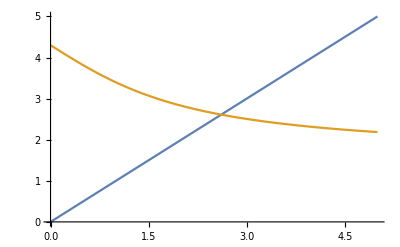

```mathematica
Plot[{x , 4.3 - 1.7*ArcTan[x/1.7]},{x,0,5}]
```

```mathematica
FindRoot[x == 4.3 - 1.7*ArcTan[x/1.7],{x,2.8}]
```

{x→2.61084}

```mathematica
D[4.3 - 1.7*ArcTan[x/1.7],x]
```

-1./(1+0.346021 x^2)

```mathematica
1./(1+(0.34602076124567477*2.6108365915442846^2))
```

0.29774

```mathematica
0.29773961929462117
```

```mathematica
funcao[x_,y_]:=Inverse[{{10.3329*x^1.67,5.1798*y^1.67},{3.4596*x^1.79,15.9309*y^1.79}}]*{1,0}
```

```mathematica
Cross[Inverse[{{10.3329*x^1.67,5.1798*y^1.67},{3.4596*x^1.79,15.9309*y^1.79}}],{1,0}]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

{{(15.9309 y^1.79)/(-17.92 x^1.79 y^1.67+164.612 x^1.67 y^1.79),-(5.1798 y^1.67)/(-17.92 x^1.79 y^1.67+164.612 x^1.67 y^1.79)},{-(3.4596 x^1.79)/(-17.92 x^1.79 y^1.67+164.612 x^1.67 y^1.79),(10.3329 x^1.67)/(-17.92 x^1.79 y^1.67+164.612 x^1.67 y^1.79)}}×{1,0}

```mathematica
q2a[x_]:=16.22 -27.68*x + 13.68*x^2 -2.0*x^3
```

```mathematica
D[q2[x],x]
D[q2[x],{x,2}]
```

-27.68+27.36 x-6. x^2

27.36-12. x

```mathematica
FindRoot[q2a[x]==0,{x,1}]
FindRoot[q2a[x]==0,{x,2}]
FindRoot[q2a[x]==0,{x,4}]
FindRoot[-27.68+27.36 x-6. x^2==0,{x,2}]
FindRoot[27.36-12. x==0,{x,2}]
Plot[q2a[x],{x,0,5}]
Plot[-27.68+27.36 x-6. x^2,{x,0,5}]
Plot[27.36-12. x,{x,0,5}]
```

{x→1.03641}

```mathematica
1.0364054145893398
```

{x→2.13024}

```mathematica
2.130237586426569
```

{x→3.67336}

{x→1.5151}

{x→2.28}

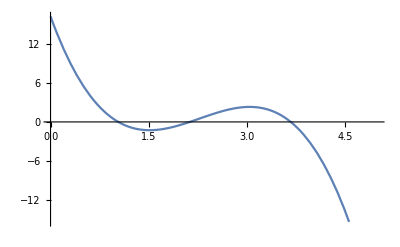

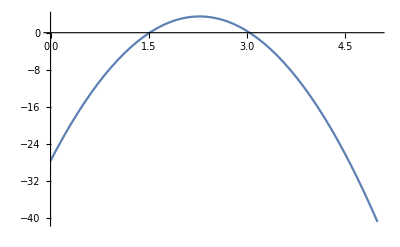

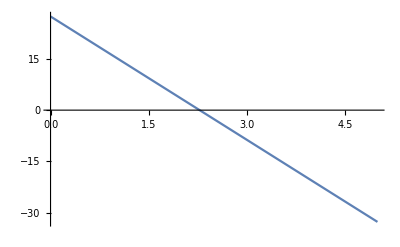

```mathematica
3.6733569989840906
```

```mathematica
FindRoot[D[q2a[x]==0,x],{x,1.5}]
FindRoot[D[q2a[x]==0,x],{x,3}]
```

{x→1.5151}

```mathematica
1.5151034928392815
```

{x→3.0449}

```mathematica
3.044896507160719
```

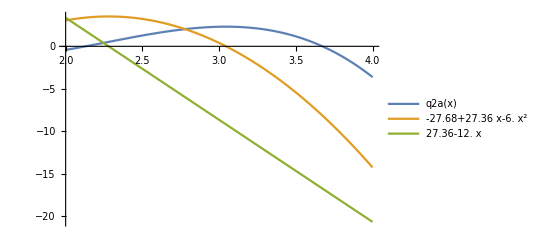

```mathematica
Plot[{q2a[x],-27.68+27.36 x-6. x^2,27.36-12. x},{x,2,4}, PlotLegends->"Expressions"]
```